Homework 5
Homework Assignment 5: Construction of a DNA neural network -  Experimental Results, Control Experiments, and DNA Degradation

Experimental Results

From lab 09, we found that the main differences between the experimental data and the simulation were when the two trajectories were fairly close. We were able to make up those differences by changing the simulation in the following ways: decrease kf and increase ks, increase kr, decrease annihilator concentration and increase ks, decrease krs and increase ks. Most of the differences would have been due to unexpected molecular behaviors, but a few could have been experimental errors.
Our proposed debugging experiments included probing the network around different steps and testing that toeholds were designed correctly. If the issue is with any of the toehold, than doing experiments directly testing those toehold would let us know if those rates were different than expected. Probing the network in different location would let us know what parts of the network the potential error effects. If we see that only one part of the network is effected, then we can narrow down the possible causes of the difference.

## CRN Simulator

Chemical Reaction Network (CRN) Simulator package is developed by David Soloveichik. Copyright 2009-2015. 
http://users.ece.utexas.edu/~soloveichik/crnsimulator.html

### Public interface specification

```mathematica
Notation`AutoLoadNotationPalette = False;
Needs["Notation`"]
BeginPackage["CRNSimulator`", {"Notation`"}];
```

```mathematica
rxn::usage="Represents an irreversible reaction. eg. rxn[a+b,c,1]";
revrxn::usage="Represents a reversible reaction. eg. revrxn[a+b,c,1,1]";
conc::usage="Initial concentration: conc[x,10] or conc[{x,y},10].";
term::usage="Represents an additive term in the ODE for species x. \
Species concentrations must be expressed in x[t] form. eg. term[x, -2 x[t]*y[t]]";
```

```mathematica
SimulateRxnsys::usage=
"SimulateRxnsys[rxnsys,endtime] simulates the reaction system rxnsys for time 0 \
to endtime. In rxnsys, initial concentrations are specified by conc statements. \
If no initial condition is set for a species, its initial concentration is set to 0. \
Rxnsys can also include term[] statements (e.g. term[x, -2 x[t]]) which are additively \
combined together with term[]s derived from rxn[] statements. \
Rxnsys can also include direct ODE definitions for some species (e.g. x'[t]==...), \
or direct definitions of species as functions of time (e.g. x[t]==...), \
which are passed to NDSolve without modification. \
Any options specified (eg WorkingPrecision->30) \
are passed to NDSolve."; 
SpeciesInRxnsys::usage=
"SpeciesInRxnsys[rxnsys] returns the species in reaction system rxnsys. \
SpeciesInRxnsys[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica pattern pttrn (eg x[1,_]).";
SpeciesInRxnsysStringPattern::usage=
"SpeciesInRxnsysPattern[rxnsys,pttrn] returns the species in reaction system rxnsys \
matching Mathematica string pattern pttrn. \
(Eg \"g$*\" matches all species names starting with \"g$\" ; \ 
can also do RegularExpression[\"o..d.\$.*\"].)";
RxnsysToOdesys::usage=
"RxnsysToOdesys[rxnsys,t] returns the ODEs corresponding to reaction system rxnsys, \
with initial conditions. If no initial condition is set for a species, its initial \
concentration is set to 0. \
The time variable is given as the second argument; if omitted it is set to Global`t.";
```

```mathematica
(*To use instead of Sequence in functions with Hold attribute but not HoldSequence,
like Module, If, etc*)
Seq:=Sequence
```

### Private

```mathematica
Begin["`Private`"];
```

```mathematica
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", OverscriptBox["→", RowBox[{" ", "k_", " "}]], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"rxn", "[", RowBox[{"r_", ",", "p_", ",", "k_"}], "]"}]]]
Notation[ParsedBoxWrapper[RowBox[{"r_", " ", UnderoverscriptBox["⇄", "k2_", "k1_"], " ", "p_", " "}]] ⟺ ParsedBoxWrapper[RowBox[{"revrxn", "[", RowBox[{"r_", ",", "p_", ",", "k1_", ",", "k2_"}], "]"}]]]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", OverscriptBox["→", RowBox[{" ", "□", " "}]], " ", "□", " "}]],"rxn"]
AddInputAlias[ParsedBoxWrapper[RowBox[{"□", " ", UnderoverscriptBox["⇄", "□", "□"], " ", "□", " "}]],"revrxn"]
```

```mathematica
(*We want rxn[a+b,c,1] to be different from rxn[b+a,c,1], so we have to set attribute
HoldAll. But we also want to evaluate if any variables can be evaluated.*)
SetAttributes[{rxn,revrxn}, HoldAll]
rxn[rs_Plus,ps_,k_]:=
 ReleaseHold[ReplacePart[rxn[1,ps,k],1->Hold[Plus]@@List@@Unevaluated[rs]]]/;
 Hold@@Unevaluated[rs] =!= Hold@@List@@Unevaluated[rs]
rxn[rs_,ps_Plus,k_]:=
 ReleaseHold[ReplacePart[rxn[rs,1,k],2->Hold[Plus]@@List@@Unevaluated[ps]]]/;
 Hold@@Unevaluated[ps] =!= Hold@@List@@Unevaluated[ps]
rxn[rs_,ps_,k_]:=
 (With[{rse=rs},rxn[rse,ps,k]])/;Head[rs]=!=Plus&&Unevaluated[rs]=!=rs
rxn[rs_,ps_,k_]:=
 (With[{pse=ps},rxn[rs,pse,k]])/;Head[ps]=!=Plus&&Unevaluated[ps]=!=ps
rxn[rs_,ps_,k_]:=
 (With[{ke=k},rxn[rs,ps,ke]])/;Unevaluated[k]=!=k
```

```mathematica
(* Automatically expand revrxn and concentration lists *)
revrxn[r_,p_,k1_,k2_]:=Sequence[rxn[r,p,k1],rxn[p,r,k2]]
conc[xs_List,c_]:=Seq@@(conc[#,c]&/@xs)

(* People are often confused about rxn[0,x,1] instead of rxn[1,x,1]. So we automatically replace any integer with 1. *)
rxn[Except[1,_Integer],ps_,k_]:=rxn[1,ps,k]
```

```mathematica
(* Species as products or reactants in rxn[] statements, as well as defined in x'[t]== or x[t]== statements \
or term statements, or conc statements *)
SpeciesInRxnsys[rxnsys_]:=
 Union[
 	Cases[Cases[rxnsys,rxn[r_,p_,_]:>Seq[r,p]]/.Times|Plus->Seq,s_Symbol|s_Symbol[__]],
 	Cases[rxnsys, x_'[_]==_ | x_[_]==_ | term[x_,__] | conc[x_,_] :> x]]
SpeciesInRxnsys[rsys_,pattern_]:=Cases[SpeciesInRxnsys[rsys],pattern]
SpeciesInRxnsysStringPattern[rsys_,pattern_]:=Select[SpeciesInRxnsys[rsys],StringMatchQ[ToString[#],pattern]&]
```

```mathematica
(* Check if a species' initial value is set in a odesys *) 	
InitialValueSetQ[odesys_,x_]:=
 MemberQ[odesys,x[_]==_]

(* Check if a species is missing an ODE or a direct definition (x[t]=_) in odesys. *)
MissingODEQ[odesys_,x_,t_Symbol]:=
 !MemberQ[odesys, D[x[t],t]==_ | x[t]==_]  	

RxnsysToOdesys[rxnsys_,t_Symbol:Global`t]:=
 Module[
  {spcs=SpeciesInRxnsys[rxnsys], concs, termssys, odesys, eqsFromTerms, eqsFromConcs},

  (* extract conc statements and sum them for same species *)
  concs = conc[#[[1,1]],Total[#[[;;,2]]]]&/@GatherBy[Cases[rxnsys,conc[__]],Extract[{1}]];

  (* Convert rxn[] to term[] statements *)
  termssys=rxnsys /. rxn:rxn[__]:>Seq@@ProcessRxnToTerms[rxn,t];

  (* ODEs from parsing terms *)
  eqsFromTerms = ProcessTermsToOdes[Cases[termssys,term[__]],t]; 
  (* initial values from parsing conc statements *)
  eqsFromConcs = Cases[concs,conc[x_,c_]:>x[0]==c]; 

  (* Remove term and conc statements from rxnsys and add eqs generated from them. 
     If there is a conflict, use pass-through equations *)
  odesys = DeleteCases[termssys, term[__]|conc[__]];
  odesys = Join[odesys,
                DeleteCases[eqsFromTerms, Alternatives@@(#'[t]==_& /@ Cases[odesys,(x_'[t]|x_[t])==_:>x])],
                eqsFromConcs];
     
  (* For species still without initial values, add zeros *)
  odesys = Join[odesys, #[0]==0& /@ Select[spcs, !InitialValueSetQ[odesys,#]&]];

  (* For species still without ODE or direct definition, add zero time derivative *)
  (* This can happen for example if conc is defined, but nothing else *)
  Join[odesys, D[#[t],t]==0& /@ Select[spcs, MissingODEQ[odesys,#,t]&]]
 ]
 
(* Create list of ODEs from parsing term statements. terms should be list of term[] statements. *) 
ProcessTermsToOdes[terms_,t_Symbol]:=
Module[{spcs=Union[Cases[terms,term[s_,_]:>s]]},
#'[t]==Total[Cases[terms,term[#,rate_]:>rate]] & /@ spcs];

(* Create list of term[] statements from parsing a rxn statement *) 
ProcessRxnToTerms[reaction:rxn[r_,p_,k_],t_Symbol]:=
Module[{spcs=SpeciesInRxnsys[{reaction}], rrate, spccoeffs,terms},
(* compute rate of this reaction *)
rrate = k (r/.{Times[b_,s_]:>s^b,Plus->Times});
(*for each species, get a net coefficient*)
spccoeffs=Coefficient[p-r,#]& /@ spcs;
(*create term for each species*)
terms=MapThread[term[#1,#2*rrate]&,{spcs, spccoeffs}];
(*change all species variables in the second arg in term[] to be functions of t*)
terms/.term[spc_,rate_]:>term[spc,rate/.s_/;MemberQ[spcs,s]:>s[t]]];
```

```mathematica
SimulateRxnsys[rxnsys_,endtime_,opts:OptionsPattern[NDSolve]]:=
 Module[{spcs=SpeciesInRxnsys[rxnsys],odesys=RxnsysToOdesys[rxnsys,Global`t]},
 Quiet[NDSolve[odesys, spcs, {Global`t,0,endtime},opts,MaxSteps->Infinity,AccuracyGoal->MachinePrecision],{NDSolve::"precw"}][[1]]]
```

```mathematica
End[];
EndPackage[];
```

## Seesaw Simulator

Seesaw Simulator package is developed by Lulu Qian.

### Define seesaw functions

The following default parameters are used:
Rate constants:
kf = 2*10^6; (fast strand displacement rate with extended toehold, unit: /M/s)
ks = 5*10^4; (slow strand displacement rate with universal toehold, unit: /M/s)
krf = 26; (fast strand dissociation rate with universal toehold, unit: /s)
krs = 1.3; (slow strand dissociation rate with extended toehold, unit: /s)
kl = 10; (strand displacement leak rate, unit: /M/s)
c = 100*10^-9; (1x standard concentration, unit: M)

Translates a seesaw gate into a list of reactions:

```mathematica
seesaw[x_,l_List,r_List,ks_:5*10^4,kf_:2*10^6,krf_:26,krs_:1.3,kl_:10]:={
(* Toehold exchange reactions *)
Outer[revrxn[w[#1,x]+g[x,w[x,#2]],g[w[#1,x],x]+w[x,#2],ks,ks]&,l,r],
(* Thresholding reactions *)
Outer[rxn[w[#,x]+th[w[#,x],x],waste,kf]&,l],
Outer[rxn[w[x,#]+th[x,w[x,#]],waste,kf]&,r],
(* Universal toehold binding reactions *)
Outer[revrxn[g[w[#,x],x]+W,g[w[#,x],x,W],kf,krf]&,l],
Outer[revrxn[g[x,w[x,#]]+W,g[W,x,w[x,#]],kf,krf]&,r],
Outer[revrxn[th[w[#,x],x]+W,th[W,w[#,x],x],kf,krs]&,l],
Outer[revrxn[th[x,w[x,#]]+W,th[x,w[x,#],W],kf,krs]&,r],
Outer[revrxn[w[#,x]+G,w[#,x,G],kf,krf]&,l],
Outer[revrxn[w[#,x]+TH,w[#,x,TH],kf,krs]&,l],
(* Leak reactions *)
Outer[rxn[g[w[#1,x],x]+w[#2,x],g[w[#2,x],x]+w[#1,x],kl]&,l,l],
Outer[rxn[g[x,w[x,#1]]+w[x,#2],g[x,w[x,#2]]+w[x,#1],kl]&,r,r]
}/.List->Sequence
```

Translates a reporter into a list of reactions and the initial concentration of the reporter:

```mathematica
reporter[x_,l_,conx_:1.5,c_:100*10^-9,ks_:5*10^4,kf_:2*10^6,krf_:26,krs_:1.3]:={
rxn[w[l,x]+Rep[x],Fluor[x],ks],
revrxn[Rep[x]+W, Rep[x,W],kf,krf],
revrxn[w[l,x]+G,w[l,x,G],kf,krf],
revrxn[w[l,x]+TH,w[l,x,TH],kf,krs],
conc[Rep[x],conx*c]
}/.List->Sequence
```

Translates logic OR operation into a list of seesaw gates and the concentrations of initial species:

```mathematica
seesawOR[x1_,x2_,l_List,r_List,c_:100*10^-9,ks_:5*10^4,kf_:2*10^6,krf_:26,krs_:1.3,kl_:10]:=
Module[{f},
{seesaw[x1,l,{x2},ks,kf,krf,krs,kl],
seesaw[x2,{x1},{r,f}],
conc[g[x1,w[x1,x2]],Length[l]*c],
Outer[conc[g[x2,w[x2,#]],1*c]&,r],
conc[w[x2,f],2*Length[r]*c],
conc[th[w[x1,x2],x2],1.1*0.6*c]
}]/.List->Sequence
```

Translates logic AND operation into a list of seesaw gates and the concentrations of initial species:

```mathematica
seesawAND[x1_,x2_,l_List,r_List,c_:100*10^-9,ks_:5*10^4,kf_:2*10^6,krf_:26,krs_:1.3,kl_:10]:=
Module[{f},
{seesaw[x1,l,{x2},ks,kf,krf,krs,kl],
seesaw[x2,{x1},{r,f},ks,kf,krf,krs,kl],
conc[g[x1,w[x1,x2]],Length[l]*c],
Outer[conc[g[x2,w[x2,#]],1*c]&,r],
conc[w[x2,f],2*Length[r]*c],
conc[th[w[x1,x2],x2],1.1*(Length[l]-1+0.2)*c]
}]/.List->Sequence
```

Translates inputs with fan-out into a list of seesaw gates and the concentrations of initial species:

```mathematica
inputfanout[x_,l_,r_List,c_:100*10^-9,ks_:5*10^4,kf_:2*10^6,krf_:26,krs_:1.3,kl_:10]:=
Module[{f},
{seesaw[x,{l},{r,f},ks,kf,krf,krs,kl],
Outer[conc[g[x,w[x,#]],1*c]&,r],
conc[w[x,f],2*Length[r]*c],
conc[th[w[l,x],x],1.1*0.2*c]
}]/.List->Sequence
```

## WTA Compiler

WTA Compiler is developed by Kevin Cherry.

### Define Reaction Functions

```mathematica
seesawAmp[x_,l_,r_List,rw_List,c_:100*10^-9,ks_:5*10^4,kf_:2*10^6,krf_:26,krs_:1.3,kl_:10]:=
Module[{f},
{seesaw[x,{l},{r,f},ks,kf,krf,krs,kl],
MapThread[conc[g[x,w[x,#1]],#2*c]&,{r,rw}],
conc[w[x,f],2*Apply[Plus,rw]*c]
}]/.List->Sequence
```

```mathematica
seesawInt[x_,l_List,r_,rw_,c_:100*10^-9,ks_:5*10^4,kf_:2*10^6,krf_:26,krs_:1.3,kl_:10]:={
seesaw[x,{l},{r},ks,kf,krf,krs,kl],
conc[g[x,w[x,r]],rw*c]
}/.List->Sequence
```

```mathematica
annihilator[l_List,x_,r_List,y_,conx_:4,c_:100*10^-9,kr1_:0.4,kr2_:0.4,kf_:2*10^6,krs_:1.3]:={
(* Toehold exchange reactions *)
Outer[revrxn[w[#,x]+A[x,y],A[w[#,x],y],kf,kr1]&,l],
Outer[revrxn[w[#,y]+A[x,y],A[w[#,y],x],kf,kr2]&,r],
Outer[rxn[w[#1,y]+A[w[#2,x],y],waste,kf]&,r,l],
Outer[rxn[w[#1,x]+A[w[#2,y],x],waste,kf]&,l,r],
(* Universal toehold binding reactions *)
revrxn[W+A[x,y],A[W,x,y],kf,krs],
revrxn[W+A[x,y],A[x,y,W],kf,krs],
revrxn[W+A[x,y,W],A[W,x,y,W],kf,krs],
revrxn[W+A[W,x,y],A[W,x,y,W],kf,krs],
Outer[revrxn[W+A[w[#,x],y],A[w[#,x],y,W],kf,krs]&,l],
Outer[revrxn[W+A[w[#,y],x],A[w[#,y],x,W],kf,krs]&,r],
(* Toehold exchange on spurious products *)
Outer[revrxn[w[#,x]+A[x,y,W],A[w[#,x],y,W],kf,kr1]&,l],
Outer[revrxn[w[#,y]+A[W,x,y],A[w[#,y],x,W],kf,kr2]&,r],
(* Complex Concentrations *)
conc[A[x,y],conx*c]
}/.List->Sequence
```

```mathematica
WTA[x_List,l_List,conx_:4,c_:100*10^-9,kr1_:0.4,kr2_:0.4,kf_:2*10^6,krs_:1.3] :={
(* Define annihilator reaction for each pair of domains *)
Table[annihilator[{l[[i]]},x[[i]],{l[[j]]},x[[j]],conx,c,kr1,kr2,kf,krs],{i,1,Length[x]-1},{j,i+1,Length[x]}]
}/.List->Sequence
```

SIMWTA takes a .csv file that contains weights and test patterns and generates a set of simulations of a DNA-based winner-take-all neural network with the given weights, each using one of the given test patterns as input. 

The following option values can be changed:

time→8 (simulation time, unit: hours) 
c→100*10^-9 (standard concentration, unit: M)

mulConc→1 (total concentration of all multiplication gates in each memory, relative to the standard concentration)
sumConc→2 (summation gate concentration relative to the standard concentration)
anhConc→4 (annihilator concentration relative to the standard concentration)
ampConc→1 (amplification gate concentration relative to the standard concentration)
repConc→2 (reporter concentration relative to the standard concentration)
sumConc, ampConc, and repConc can also be defined as a list, e.g. sumConc→{1,2}, if different gates/reporters of the same type have different concentrations.

kr→0.4 (strand dissociation rate on an annihilator, unit: /s)
kr can also be defined as a list, e.g. kr→{1, 0.4}, if the dissociation rates on two sides of the annihilator are different. 

mulks→5*10^4  (strand displacement rate of the multiplication gates, unit: /M/s)
sumks→5*10^4  (strand displacement rate of the summation gates, unit: /M/s)
ampks→5*10^4  (strand displacement rate of the amplification gates, unit: /M/s)
repks→5*10^4  (strand displacement rate of the reporters, unit: /M/s)
sumks, ampks, and repks can also be defined as a list, e.g. sumks→{5*10^4, 10^5}, if different gates/reporters of the same type have different rates.

kf→2*10^6 (strand displacement rate of annihilation, unit: /M/s)
krf→26 (strand dissociation rate on a gate, unit: /s)
krs→1.3 (strand dissociation rate on a threshold, unit: /s)
mulkl→10 (strand displacement rate of leak reactions between a gate and fuel in the multiplication layer, unit: /M/s) 
ampkl→10 (strand displacement rate of leak reactions between a gate and fuel in the amplification layer, unit: /M/s) 

To simulate a set of control experiments, use inputSignal→False and controlSignal→{sample1, sample2, etc.}
each sample = {species1, species2, etc.}
each species = {species name, relative concentration}

```mathematica
Options[SIMWTA]={time->8,c->100*10^-9,
mulConc->1,sumConc->2,anhConc->4,ampConc->1,repConc->2,
kr->0.4,kf->2*10^6,krf->26,krs->1.3,mulkl->10,ampkl->10,
mulks->5*10^4,sumks->5*10^4,ampks->5*10^4,repks->5*10^4,
multiplication->Range[101,200],summation->{15,4},amplification->{16,7},reporting->{6,23},
inputSignal->True,controlSignal->{}};
SIMWTA[fileName_,OptionsPattern[]]:=Module[{inputfile,memory,test,header,data,memoryNorm,nMems,nBits,rsys,input},

SetDirectory[NotebookDirectory[]];
inputfile=Import[fileName];
header=inputfile[[1]];
data=Transpose[inputfile[[2;;]]];

memory={};
test={};

For[i=1,i<=Length[header],i++,
If[StringTake[header[[i]],6]=="memory",AppendTo[memory,data[[i]]]];
If[StringTake[header[[i]],4]=="test",AppendTo[test,data[[i]]]];
]; 

(* Normalize each memory to sum to 1x *)
memoryNorm=Map[#/Total[Cases[#,n_/;n>0]]&,memory];

nMems = Length[memory];

nBits=Length[Position[test[[1]],1]];

rsys=Flatten@{
(* Creates list of input seesaw gates for multiplying inputs *)
Table[seesawAmp[OptionValue[multiplication][[n]],h,OptionValue[summation],memoryNorm[[;;,n]]*OptionValue[mulConc],OptionValue[c],OptionValue[mulks],OptionValue[kf],OptionValue[krf],OptionValue[krs],OptionValue[mulkl]],{n,Union[Flatten@Table[Position[memory[[i]],_?Positive],{i,nMems}]]}],

(* Creates the seesaw integration gates for computing the weighted sum *)
Table[
seesawInt[OptionValue[summation][[i]],Table[OptionValue[multiplication][[n]],{n,Union[Flatten@Table[Position[memory[[i]],_?Positive],{i,nMems}]]}],OptionValue[amplification][[i]],If[Length[OptionValue[sumConc]]==nMems,OptionValue[sumConc][[i]],OptionValue[sumConc]],OptionValue[c],If[Length[OptionValue[sumks]]==nMems,OptionValue[sumks][[i]],OptionValue[sumks]],OptionValue[kf],OptionValue[krf],OptionValue[krs]],
{i,nMems}],

(* Creates the seesaw gates and annihilators for WTA computation *)
WTA[OptionValue[amplification],OptionValue[summation],OptionValue[anhConc],OptionValue[c],
If[Length[OptionValue[kr]]==2,OptionValue[kr][[1]],OptionValue[kr]],
If[Length[OptionValue[kr]]==2,OptionValue[kr][[2]],OptionValue[kr]],
OptionValue[kf],OptionValue[krs]],

(* Creates the seesaw amplification gates for restoring the winning signal *)
Table[
seesawAmp[OptionValue[amplification][[i]],OptionValue[summation][[i]],{OptionValue[reporting][[i]]},{If[Length[OptionValue[ampConc]]==nMems,OptionValue[ampConc][[i]],OptionValue[ampConc]]},OptionValue[c],If[Length[OptionValue[ampks]]==nMems,OptionValue[ampks][[i]],OptionValue[ampks]],OptionValue[kf],OptionValue[krf],OptionValue[krs],OptionValue[ampkl]],
{i,nMems}],

(* Creates the seesaw reporters *)
Table[
reporter[OptionValue[reporting][[i]],{OptionValue[amplification][[i]]},If[Length[OptionValue[repConc]]==nMems,OptionValue[repConc][[i]],OptionValue[repConc]],OptionValue[c],If[Length[OptionValue[repks]]==nMems,OptionValue[repks][[i]],OptionValue[repks]]],
{i,nMems}],

(* Creates reactions to simulate binding to shared toehold sequences *)
conc[W,(2*Total[Select[Flatten[memoryNorm],#>0&]]+1+2*nMems)*OptionValue[c]],
conc[G,(Total[Select[Flatten[memoryNorm],#>0&]]+nMems*(1+1+2))*OptionValue[c]],
conc[TH,(2*Binomial[nMems,2]-nMems+1)*OptionValue[c]]
};

If[OptionValue[inputSignal],
Table[
(* Defines input strands for each test case *)
input=Table[conc[w[h,OptionValue[multiplication][[n]]],1/nBits*OptionValue[c]],{n,Flatten@Position[xs,1]}];

sol=SimulateRxnsys[Join[rsys,input],OptionValue[time]*60*60];

(* Return the simulated concentration for these species *)
Table[Fluor[OptionValue[reporting][[i]]][t*60*60]/10^-9/.sol,{i,nMems}],

(* Loop over these test cases *)
{xs,test}],

Table[
input=Table[conc[s[[1]],s[[2]]*OptionValue[c]],{s,species}];

sol=SimulateRxnsys[Join[rsys,input],OptionValue[time]*60*60];

(* Return the simulated concentration for these species *)
Table[Fluor[OptionValue[reporting][[i]]][t*60*60]/10^-9/.sol,{i,nMems}],

(* Loop over controls *)
{species,OptionValue[controlSignal]}]]]
```

## Protocol generator

RoundToPipet converts an arbitrary volume vol (unit: uL) to a pipet volume by rounding it to the nearest multiple of the appropriate increment based on the range it belongs to.

```mathematica
RoundToPipet[vol_]:=Which[
vol≤2,Round[vol/2,0.001]*2,
vol≤20,Round[vol/2,0.01]*2,
vol≤200,Round[vol/2,0.1]*2,
vol≤5000,Round[vol,1]]
```

Anneal generates a protocol for mixing two single strands that will then be annealed into a double-stranded complex on a thermal cycler (note: a typical annealing schedule is to hold at 90 °C for 2 min, 90 to 20 °C @ 1 °C/min, and then hold at 20 °C until the sample is taken out from the cycler).
complex is the name of a double-stranded complex to be annealed, represented as a string. 
vol is the target volume (unit: uL) of the annealed complex, represented as a number.
The name, stock concentration, and target concentration of the two strands are given as strand1, conc1stock, conc1target, strand2, conc2stock, and conc2target. The units of all concentrations are uM.

```mathematica
Anneal[complex_,vol_,strand1_,conc1stock_,conc1target_,strand2_,conc2stock_,conc2target_]:=Module[
{vol1,vol2,vol3,vol4},
vol1=conc1target*vol/conc1stock; (* pipetting volume of strand1 *)
vol2=conc2target*vol/conc2stock; (* pipetting volume of strand2 *)
vol3=vol/10; (* pipetting volume of 1×TE/10×Mg^(2+) *)
vol4=vol-vol1-vol2-vol3; (* pipetting volume of 1×TE *)
Grid[{{"Name","Concentration(uM)", "Volume(uL)"},
{"1×TE","",RoundToPipet[vol4]},
{"1×TE/10×Mg^(2+)","",RoundToPipet[vol3]},
{strand1,conc1stock,RoundToPipet[vol1]},
{strand2,conc2stock,RoundToPipet[vol2]},
Style[#,Bold]&/@{complex,Min[conc1target,conc2target],vol}},
Alignment->Right,Frame->All,
Background->{None,{-1->LightGray}}]]
```

Dilute generates a protocol for diluting a strand.
strand is the name of a strand to be diluted, represented as a string. 
vol is the target volume (unit: uL) of the diluted strand, represented as a number.
concstock and conctarget are stock and target concentrations (unit: uM) of the strand.

```mathematica
Dilute[strand_,vol_,concstock_,conctarget_]:=Module[
{vol1,vol2},
vol1=conctarget*vol/concstock; (* pipetting volume of strand *)
vol2=vol-vol1; (* pipetting volume of 1×TE *)
Grid[{{"Name","Concentration(uM)", "Volume(uL)"},
{"1×TE","",RoundToPipet[vol2]},
{strand,concstock,RoundToPipet[vol1]},
Style[#,Bold]&/@{strand,conctarget,vol}},
Alignment->Right,Frame->All,
Background->{None,{-1->LightGray}}]]
```

Mix generates a protocol for mixing buffer and a list of  DNA species for hybridization or strand displacement reactions.
vol is the target volume (unit: uL) of the mix, represented as a number.
specieslist is a list of single- or double-stranded DNA molecules, each element of which is a list that includes the name, stock concentration, and target concentration of a species. All names are represented as strings, and the units of all concentrations are uM.
samplename is the name of the sample, represented as a string.  The default is “Total”.
Option NoInput removes the input strand, assuming that it is the last species in the specieslist, from the displayed protocol. The default is False.
Option DisplayProtocol specifies if the protocol is displayed. The default is True. When using the Mix function to calculate the volume of the mix without the input strand, this option should be set to False.

```mathematica
Options[Mix]={NoInput->False,DisplayProtocol->True};
SetAttributes[Mix,HoldFirst]; (* this allows the volume to be changed if the input strand is to be removed *)
Mix[vol_,specieslist_,samplename_:"Total",OptionsPattern[]]:=Module[
{vollist,volDS,volNoInput},
vollist=Table[specieslist[[i,3]]*vol/specieslist[[i,2]],{i,Length[specieslist]}]; (* pipetting volume of each species *)
volDS=Sum[If[specieslist[[i,4]]=="ds",vollist[[i]],0],{i,Length[vollist]}];
(* total volume of all double-stranded species *)
AppendTo[vollist,(vol-volDS)/10]; (* pipetting volume of 1×TE/10×Mg^(2+) *)
AppendTo[vollist,vol-Total[vollist]]; (* pipetting volume of 1×TE *)
vollist=Table[RoundToPipet[vollist[[i]]],{i,Length[vollist]}];
(* round all volumes to pipet volumes *)
If[OptionValue[NoInput],vol=vol-vollist[[-3]]];
(* if the input strand is to be removed from the mix, subtract its volume from the total volume *)
If[OptionValue[DisplayProtocol],
Grid[Join[
{{"Name","Concentration(uM)", "Volume(uL)"},
{"1×TE","",vollist[[-1]]},
{"1×TE/10×Mg^(2+)","",vollist[[-2]]}},
Table[{specieslist[[i,1]],specieslist[[i,2]],vollist[[i]]},{i,Length[specieslist]-If[OptionValue[NoInput],1,0]}],
{Style[#,Bold]&/@{samplename,"",vol}}],
Alignment->Right,Frame->All,
Background->{None,{-1->LightGray}}]]]
```

MasterMix generates a protocol for making a master mix that combines the shared DNA species in multiple samples of a strand-displacement circuit.
vol is the target volume (unit: uL) of all samples, assuming that they are identical.
specieslist is a list of single- or double-stranded DNA molecules, each element of which is a list that includes the name, stock concentration, and target concentration of a species. All names are represented as strings, and the units of all concentrations are uM.
sampleNumber is the number of samples.
excessRatio is the ratio of the master mix volume to the total volume of all samples.

```mathematica
MasterMix[vol_,specieslist_,sampleNumber_,excessRatio_]:=Module[{masterVol},
masterVol=vol*sampleNumber*excessRatio;
Mix[masterVol,specieslist,"Master mix",NoInput->True]]
```

RemainderMix generates a protocol for making multiple samples using a master mix.
vol is the target volume (unit: uL) of all samples, assuming that they are identical.
specieslist is a list of single- or double-stranded DNA molecules, each element of which is a list that includes the name, stock concentration, and target concentration of a species. All names are represented as strings, and the units of all concentrations are uM. The input strand is the last species in the list, whose target concentration is represented as a list of target input concentrations in all samples.
samplelist is a list of sample names.

```mathematica
RemainderMix[vol_,specieslist_,samplelist_]:=Module[
{maxInput,specieslistMaxInput,vollist,volMastermix=vol,volInput,volTE},
maxInput=Max[specieslist[[-1,3]]];
specieslistMaxInput=Join[specieslist[[;;-2]],
{{specieslist[[-1,1]],specieslist[[-1,2]],maxInput,specieslist[[-1,4]]}}];
Mix[volMastermix,specieslistMaxInput,"Master mix",NoInput->True,DisplayProtocol->False];
volInput=Table[RoundToPipet[specieslist[[-1,3,i]]*vol/specieslist[[-1,2]]],{i,Length[specieslist[[-1,3]]]}];
volTE=Table[RoundToPipet[vol-volMastermix-volInput[[i]]],{i,Length[volInput]}];
Grid[{{"Name","Concentration(uM)",ConstantArray[ "Volume(uL)",Length[volInput]]}//Flatten,
{"Master mix", "",ConstantArray[RoundToPipet[volMastermix],Length[volInput]]}//Flatten,
{"1×TE","",volTE}//Flatten,
{specieslist[[-1,1]],specieslist[[-1,2]],volInput}//Flatten,
{"","",Style[#,Bold]&/@samplelist}//Flatten},
Alignment->Right,Frame->All,
Background->{None,{-1->LightGray}}]]
```

## Weighted sum analysis functions

weightedSum function computes the weighted sum of an input pattern for any given weight matrix, and normalize the weighted sum by dividing it by the sum of all weights in the weight matrix.

```mathematica
weightedSum[input_,weight_]:=input.weight/Total[weight];
```

margin function computes the difference between two weighted sums for any input pattern with a given class label and two given weight matrices stored in a list weights.

```mathematica
margin[input_,class_,weights_]:=(weightedSum[input,weights[[1]]]-weightedSum[input,weights[[2]]])*If[class==1,1,-1]
```

weightedSumAnalysis function displays a set of test patterns of two classes stored in a list tests in their weighted sum space, given two weight matrices stored in a list weights. 
Two options are available: 
testName defines whether the name of each test pattern is shown. The default is False. 
weightsColor defines the colors of the two weight matrices. The default is Blue and Orange.

```mathematica
Options[weightedSumAnalysis]={testName->False,weightsColor->{Blue,Orange}};
weightedSumAnalysis[tests_,weights_,OptionsPattern[]]:=Module[{weightedSumList,minMargin,colors},
colors=OptionValue[weightsColor];
weightedSumList=Table[
Callout[
{weightedSum[tests[[i,j]],weights[[2]]],weightedSum[tests[[i,j]],weights[[1]]]},
displayData[tests[[i,j]],grid->False,
label->If[OptionValue[testName],"x"<>ToString[i]<>","<>ToString[j],""]],
LabelVisibility->All],
{i,2},{j,Length[tests[[i]]]}];
minMargin=Min[Table[margin[tests[[i,j]],i,weights],{i,2},{j,Length[tests[[i]]]}]//Flatten];
Labeled[Show[ListPlot[weightedSumList,PlotStyle->Table[{PointSize[Large],colors[[i]]},{i,2}],
Frame->True,FrameLabel->{"s_2", "s_1"},PlotLabel->Row[{"minimum margin = ",Round[minMargin,0.01]}],
PlotRange->{{-0.05,1.05},{-0.05,1.05}},
AspectRatio->1,GridLines->Full,LabelStyle->16,ImageSize->450],
Graphics[Line[{{0,0},{1,1}}]]],
Grid[Table[{displayData[weights[[i]],color->colors[[i]],label->"w"<>ToString[i]]},{i,2}]],Right]
]
```

## Load and display data functions

excelLoad function reads an excel data file from a Synergy H1 plate reader, that contains two fluorescence datasets with distinct excitation and emission wavelengths, and generates two corresponding data lists in the format of {time, raw fluorescence}.
fileName is a string of the name of the data file including its extension (e.g. fileName = “data1.xlsx”).
col has two lists that each contains the left and right Excel column names of a dataset given as strings. For two fluorescence datasets of the same samples, these two lists are identify (e.g. col = {{“B”,“CU”},{“B”,“CU”}} covers all 96 samples in a plate).
row has two lists that each contains the top and bottom Excel rows of a dataset given as numbers, excluding the header.
delay is the delay time between the sample was mixed and the measurement was started (unit: hours).

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
excelLoad[fileName_,col_,row_,delay_]:=
Module[{rowRange,colRange,data,timeUnits,dataList},

rowRange=Range@@@row; 
colRange=Range@@@(Map[FromDigits[#,26]&,LetterNumber[Characters[col]],{2}]);

(*Load the Excel data*)
data=Import[fileName,{"Data",1,rowRange[[#]],Delete[colRange[[#]],2]}]&/@Range[Length[row]]; 

(* Rearrange data, Convert time stamps *)
(* Put data in (x, y) pairs of (time, value) *)
timeUnits=1/60/60; (* converts time to hours *)
dataList=Table[{N[(AbsoluteTime[data[[#]][[i]][[1]]]-AbsoluteTime[data[[#]][[1]][[1]]])*timeUnits+delay],data[[#]][[i]][[j]]},{j,2,Dimensions[data][[3]]},{i,Dimensions[data][[2]]}]&/@Range[Length[row]];

(*Return reshaped data*)
dataList]
```

NormalizeDataList function takes a list of raw fluorescence data and normalizes it to a list of output concentrations. 
datalist is a list of trajectories, each containing a list of data points in the format of {time, raw fluorescence}.
referencelist is a list of reference points used for normalization. The format is {trajectory number in datalist, reference points = 0 (first 5 data points) or 1 (last 5 data points), concentration}.
Average raw fluorescence levels are extracted from the datalist based on the referencelist, giving a list of pairs {average raw fluorescence, concentration} that incorporates the reference points from all the trajectories. A linear fit y=a+bx, where x is raw fluorescence and y is concentration, provides a consistent way to map raw fluorescence to concentration for all data points in all trajectories.

```mathematica
NormalizeDataList[datalist_,referencelist_]:=Module[{ref,start,end,normF},
ref=Table[
If[referencelist[[i,2]]==0, 
start=1;end=5,
start=Length[datalist[[referencelist[[i,1]]]]]-4;end=Length[datalist[[referencelist[[i,1]]]]]];
{Mean[Table[datalist[[referencelist[[i,1]],j,2]],
{j,start,end}]],referencelist[[i,3]]},{i,1,Length[referencelist]}];
normF=LinearModelFit[ref,x,x];
Table[{datalist[[i,j,1]],normF[datalist[[i,j,2]]]},
{i,1,Length[datalist]},{j,1,Length[datalist[[1]]]}]]
```

PlotData function takes a list of data and plots multiple kinetics trajectories over time.
datalist is a list of trajectories, each containing a list of data points in the format of {time, raw fluorescence} or {time, concentration}.
trajectories is a list of species names or concentrations shown in the legend.
TrajectoryLabel is a label for the legend of trajectories. 
OutputLabel is a label for the vertical axis, which should be a description of the output measured. The unit of the data points should also be specified here. 
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range.  The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit for raw data is arbitrary fluorescence level (a.u.). The unit for normalized data is nM. Same format and default as timeRange.

```mathematica
Options[PlotData]={plotSize->300,labelSize->16,pointSize->0.02};
PlotData[datalist_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All,OptionsPattern[]]:=
ListPlot[datalist,PlotLabel->Style[CircuitLabel,OptionValue[labelSize]],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->Table[{PointSize[OptionValue[pointSize]],ColorData["Rainbow"][i]},
{i,If[Length[datalist]<8,0.12,0],0.96,0.96/Length[datalist]}],
PlotLegends->Placed[SwatchLegend[Automatic,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->OptionValue[labelSize]*0.75],Right],
LabelStyle->Directive[Gray,FontSize->OptionValue[labelSize],FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->OptionValue[plotSize]]
```

PlotSim function plots a simulation including multiple trajectories.
SIMcircuit is a simulation.
SIMtime is the simulation time.  
trajectories is a list of species names or concentrations shown in the legend. The default is none.
TrajectoryLabel is a label for the legend of trajectories. The default is none.
OutputLabel is a label for the vertical axis, which should be a description of the output simulated, with unit specified. The default is none.
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range. The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit is nM. Same format and default as timeRange.

```mathematica
Options[PlotSim]={plotSize->300,labelSize->16,lineThickness->2};
PlotSim[SIMcircuit_,SIMtime_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All,OptionsPattern[]]:=
Plot[SIMcircuit,{t,0,SIMtime},PlotLabel->Style[CircuitLabel,OptionValue[labelSize]],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->Table[{AbsoluteThickness[OptionValue[lineThickness]],ColorData["Rainbow"][i]},{i,If[Length[SIMcircuit]<8,0.12,0],0.96,0.96/Length[SIMcircuit]}],
PlotLegends->Placed[SwatchLegend[Automatic,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->OptionValue[labelSize]*0.75],Right],
LabelStyle->Directive[Gray,FontSize->OptionValue[labelSize],FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->OptionValue[plotSize]]
```

displayData function takes a 100-bit pattern stored in a single non-nested list data and shows it on a 10 by 10 grid. The pattern may be binary (zeros and ones) or analog (values between zero and one). 
Three options are available: 
color defines the color of the pattern. The default is Black.
label is a string that defines the text shown above the pattern. The default is “” (i.e. no label).
grid defines whether the grid lines are shown. The default is True.

```mathematica
Options[displayData]={color->Black,label->"",grid->True,size->100};
displayData[data_,OptionsPattern[]]:=Module[{colorScale},
colorScale[x_]:=Lighter[OptionValue[color],1-x];
ArrayPlot[Partition[data,10],Mesh-> If[OptionValue[grid],All,None],ColorFunction->colorScale,
PlotLabel->If[OptionValue[label]≠"",OptionValue[label],None],ImageSize->OptionValue[size]]]
```

## Load weights and tests

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["DNA_and_Caltech_Lab09.csv"];
```

```mathematica
weights=Table[data[[2;;,i]],{i,2}];
```

```mathematica
tests=Table[data[[2;;,2+(i-1)*8+j]],{i,2},{j,8}];
```

```mathematica
weightsPlot=Grid[{Table[displayData[weights[[i]],label->If[i==1,"w1","w2"],color->If[i==1,Blue,Orange]],{i,2}]}]
```

-Graphics- | -Graphics-

```mathematica
testsPlot=Grid[Table[displayData[tests[[i,j]],label->"test["<>ToString[i]<>","<>ToString[j]<>"]"],{i,2},{j,8}]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
weightedSumAnalysisPlot=weightedSumAnalysis[tests,weights]
```

-Graphics--Graphics-
-Graphics-

```mathematica
Export["weights.png",weightsPlot];
Export["tests.png",testsPlot];
Export["weightedSumAnalysis.png",weightedSumAnalysisPlot];
```

## Data analysis

```mathematica
datafileName="Lab09_data.xlsx";
col={{"B","AV"},{"B","AV"}};
row={{47,406},{411,770}};
delay=15/60;
dataList=excelLoad[datafileName,col,row,delay];
```

The samples with test[1,1] through test[1,8] were in wells A1 through A8, and the samples with test[2,1] through test[2,8] were in wells A9 through B4. Control samples were in wells B5 through D5, and calibration samples were in wells D6 through D9.

-Graphics-

The following control experiments were performed:

3× signal on an input wire to the first summation gate

3× signal on an input wire to the second summation gate

3× signals on two input wires, one going to each of the two summation gates

1× signals on two input wires each to one of the two summation gates

2× signal on an output wire of the first summation gate

2× signal on an output wire of the second summation gate

2× signals on two output wires, one coming out of each of the two summation gates

1× signals on two output wires, one coming out of each of the two summation gates

Signals on two input wires, one going to each of the two summation gates, at concentrations equal to the two weighted sums of test[1,2].

Signals on two output wires, one coming out of each of the two summation gates, at concentrations equal to the two weighted sums of test[1,2].

Signals on two input wires, one going to each of the two summation gates, at concentrations equal to the two weighted sums of test[2,2].

Signals on two output wires, one coming out of each of the two summation gates, at concentrations equal to the two weighted sums of test[2,2].

Signals on two input wires, one going to each of the two summation gates, at concentrations equal to the two weighted sums of test[1,8].

Signals on two output wires, one coming out of each of the two summation gates, at concentrations equal to the two weighted sums of test[1,8].

Signals on two input wires, one going to each of the two summation gates, at concentrations equal to the two weighted sums of test[2,7].

Signals on two output wires, one coming out of each of the two summation gates, at concentrations equal to the two weighted sums of test[2,7].

0.05× signals on all input wires, one going to each of the 100 weight multiplication gates.

1× signal on an input wire to the 25th weight multiplication gate, which has a gate concentration that corresponds to the fourth largest value in w_1.

1× signal on an input wire to the 84th weight multiplication gate, which has a gate concentration that corresponds to the third largest value in w_1.

1× signal on an input wire to the 36th weight multiplication gate, which has a gate concentration that corresponds to the second largest value in w_1.

1× signal on an input wire to the 17th weight multiplication gate, which has a gate concentration that corresponds to the largest value in w_1.

1× signal on an input wire to the 75th weight multiplication gate, which has a gate concentration that corresponds to the fourth largest value in w_2.

1× signal on an input wire to the 6th weight multiplication gate, which has the third largest value in w_2.

1× signal on an input wire to the 15th weight multiplication gate, which has a gate concentration that corresponds to the second largest value in w_2.

1× signal on an input wire to the 77th weight multiplication gate, which has a gate concentration that corresponds to the largest value in w_2.

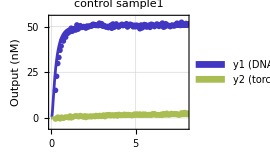
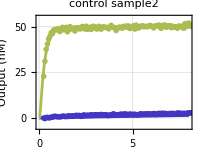
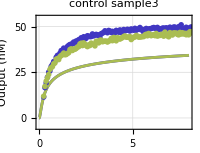
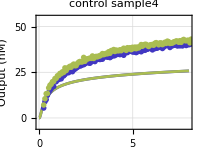
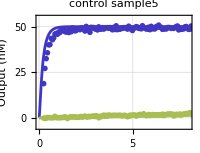
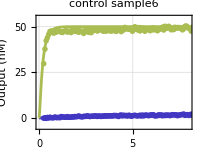
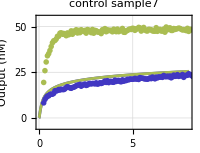
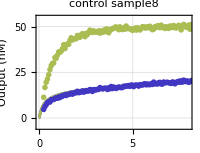
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

For reference, the circuit diagram is shown here:

-Graphics-

The species name and relative concentration of each control experiment are defined as follows:

```mathematica
controls={
{{w[185,15],3}}, 
{{w[185,4],3}},
{{w[185,15],3},{w[185,4],3}},
{{w[185,15],1},{w[185,4],1}}, 
{{w[15,16],2}}, 
{{w[4,7],2}},
{{w[15,16],2},{w[4,7],2}},
{{w[15,16],1},{w[4,7],1}},
{{w[185,15],0.726},{w[185,4],0.087}},
{{w[15,16],0.726},{w[4,7],0.087}},
{{w[185,15],0.267},{w[185,4],0.884}},
{{w[15,16],0.267},{w[4,7],0.884}},
{{w[185,15],0.369},{w[185,4],0.156}},
{{w[15,16],0.369},{w[4,7],0.156}},
{{w[185,15],0.343},{w[185,4],0.502}},
{{w[15,16],0.343},{w[4,7],0.502}},
Table[{w[h,x],0.05},{x,101,200}],
{{w[h,125],1}},
{{w[h,184],1}},
{{w[h,136],1}},
{{w[h,117],1}},
{{w[h,175],1}},
{{w[h,106],1}},
{{w[h,115],1}},
{{w[h,177],1}}
};
```

Plot raw fluorescence data of the 25 control experiments. The two fluorescence channels corresponding to Fluor6 and Fluor23 are plotted separately, while trajectories from all 16 samples are shown in the same plot.

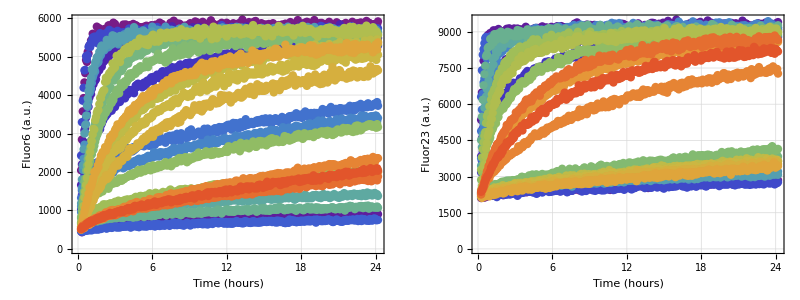

```mathematica
OutputLabel={"Fluor6 (a.u.)","Fluor23 (a.u.)"}; 
Grid[{Table[PlotData[dataList[[f,17;;41]],"","",OutputLabel[[f]]],
{f,2}]}]
```

Normalize raw fluorescence data to concentration data, using reference points in the data trajectories for the 5th and 6th control samples. These two samples each have a signal from a summation gate to an amplification gate directly connected to a reporter. We assume that the first 5 data points for the 6th control sample corresponds to y1=0 and the last 5 data points for the 5th control sample corresponds to y1=1 (i.e. 50 nM); the first 5 data points for the 5th control sample corresponds to y2=0 and the last 5 data points for the 6th control sample corresponds to y2=1 (i.e. 50 nM).

```mathematica
referencelist={{{16+6,0,0},{16+5,1,50}},{{16+5,0,0},{16+6,1,50}}};
dataListNorm=Table[NormalizeDataList[dataList[[f]],referencelist[[f]]],{f,2}];
```

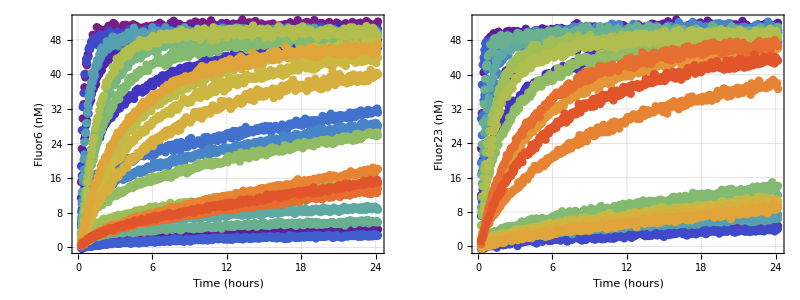

```mathematica
OutputLabel={"Fluor6 (nM)","Fluor23 (nM)"}; 
Grid[{Table[PlotData[dataListNorm[[f,17;;41]],"","",OutputLabel[[f]]],
{f,2}]}]
```

Plot normalized data of the control experiments that you are interested in. For example,  the normalized data of the 5th and 6th control experiments are displayed as follows:

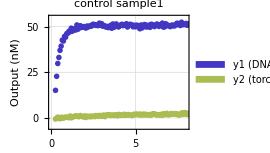
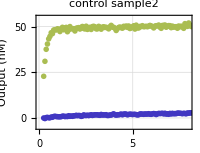
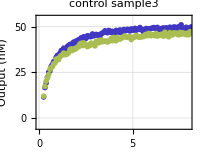
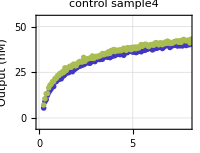
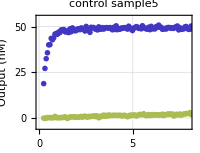
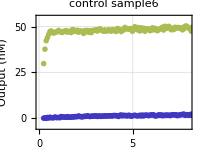
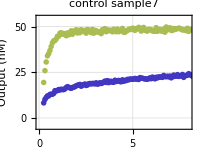
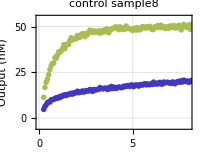
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
samples=Range[1,25];
OutputLabel="Output (nM)";
CircuitLabel=Table["control sample"<>ToString[s],{s,25}];
TimeRange={0,8};
OutputRange={-5,55};
Legended[Grid[Partition[Table[
PlotData[dataListNorm[[;;,s+16]],"","",OutputLabel,CircuitLabel[[s]],TimeRange,OutputRange,plotSize->200],
{s,samples}],UpTo[4]]],
SwatchLegend[Directive[ColorData["Rainbow"][#]]&/@{0.12,0.12+0.96/2},{"y1 (DNA)","y2 (torch)"},
LabelStyle->16]]
```

Perform simulation of the control experiments that you are interested in. For example,  simulation for the 5th and 6th control experiments are displayed as follows:

SIMWTA is defined in WTA Compiler above, now with more options provided.

```mathematica
fileName="DNA_and_Caltech_Lab09.csv";
SIMcircuit=SIMWTA[fileName,c->50*10^-9,
inputSignal->False,controlSignal->Table[controls[[s]],{s,samples}]];
```

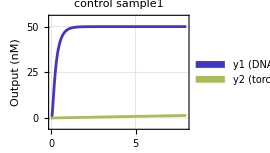
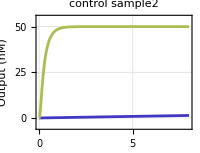
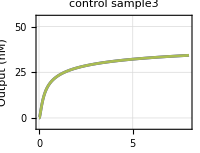
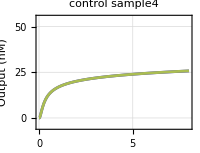
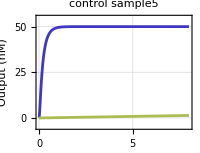
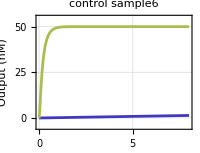
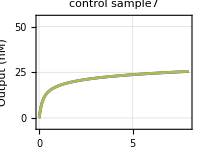
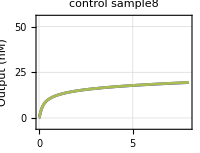
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
SIMtime=8;
OutputLabel="Output (nM)";
CircuitLabel=Table["control sample"<>ToString[s],{s,25}];
TimeRange={0,8};
OutputRange={-5,55};
Legended[Grid[Partition[Table[
PlotSim[SIMcircuit[[s]],SIMtime,"","",OutputLabel,CircuitLabel[[samples[[s]]]],TimeRange,OutputRange,plotSize->200],
{s,Length[samples]}],UpTo[4]]],
SwatchLegend[Directive[ColorData["Rainbow"][#]]&/@{0.12,0.12+0.96/2},{"y1 (DNA)","y2 (torch)"},
LabelStyle->16]]
```

Display normalized data overlaid with simulation.

```mathematica
Legended[Grid[Partition[Table[Show[
PlotSim[SIMcircuit[[s]],SIMtime,"","",OutputLabel,CircuitLabel[[samples[[s]]]],TimeRange,OutputRange,plotSize->200],
PlotData[dataListNorm[[;;,samples[[s]]+16]]]],
{s,Length[samples]}],UpTo[4]]],
SwatchLegend[Directive[ColorData["Rainbow"][#]]&/@{0.12,0.12+0.96/2},{"y1 (DNA)","y2 (torch)"},
LabelStyle->16]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

Control Experiments

These control experiments indicate that the problem is with the annihilator step or later, as all of the test still have a difference between the simulation and the data with this error being more significant when the trajectories are closer. This means that any part of the hypothesis that could effect any of those steps could be the reason for the difference. Another part of the hypothesis that this helps clarify, is that the issue is due to unexpected molecular behavior as opposed to experimental error, since this error is present within all of the control experiments. This means it isn’t an error in annihilator concentration, but could still be an issue with any of the rates having to do with the annihilation, signal restoration, or reporting. Additional experiments that we could perform would be running more control experiments to test only the sections after annihilation (signal restoration + reporting or just reporting). If these control experiment line up with the simulations for them, then the error would be due to rates just effecting annihilation (similar for signal restoration), otherwise we would know that one of rates that effects signal restoration or reporting.

DNA Degradation

Three other types of damaged double-stranded complexes that may exist include summation gate, weight (for weight multiplication), and annihilator.
Weight: If the weight has a damaged base within the single-stranded branch migration domain, then the intermediate product will react with the summation gate at a much slower rate (or will be unable to displace the stand). This would slow down the entire set of reactions and possibly have other downstream effects.
Summation Gate: If the summation gate has a damaged base within the single-stranded branch migration domain, then it will react with the annihilator at a much slower rate (or will be unable to displace the stand) and will also react with the restoration gate at a much slower rate (or will be unable to displace the stand).
Annihilator: If the annihilator has a damaged base, then the weighted sum migration might happen at a faster rate and the reverse migration might happen at a slower rate. This could slow down the signal amplification as the weighted sum would be bound to the annihilator more often.